```mathematica
L[μ_,b_]:=(b+μ*s)^n*Exp[-(b+μ*s)]*b^m*Exp[-b]
L[μ,b]
L[0,(n+m)/2]
q0[μ_,b_]:=FullSimplify[-2*PowerExpand@Log[L[0,(n+m)/2]/L[μ,b]]]
q0[μ,b]
a0[μ_,b_]:=FullSimplify[q0[μ,b]/.{n->m+μ*s}]
a0[μ,b]
```

b^m ⅇ^(-2 b-s μ) (b+s μ)^n

(2 ⅇ)^(-m-n) (m+n)^(m+n)

-2 (2 b-n+s μ-m (1+Log[2])-m Log[b]+(m+n) Log[m+n]-n Log[2 (b+s μ)])

-2 (2 b-m (2+Log[2])-m Log[b]-(m+s μ) Log[2 (b+s μ)]+(2 m+s μ) Log[2 m+s μ])

```mathematica
1bin case, bhat=m
```

```mathematica
t[μ_]:=a0[μ,b]/.b->m/.{m->100,s->1}
FullSimplify[t[μ]]
```

-2 (-100 Log[200]-(100+μ) Log[2 (100+μ)]+(200+μ) Log[200+μ])

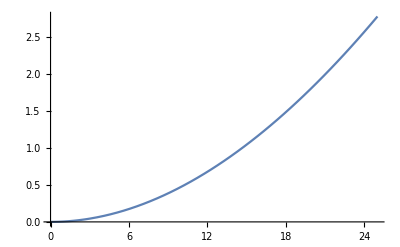

```mathematica
Plot[t[μ],{μ,0,25}]
```

```mathematica
FindRoot[t[μ]-1,{μ,0,25}]
```

{μ→14.6451}

```mathematica
L[μ_,b_]:=(b+μ*s)^B*Exp[-(b+μ*s)]*b^A*Exp[-b]
q0[μ_,b_]:=FullSimplify[-2*PowerExpand@Log[L[0,(A+B)/2]/L[μ,b]]]
q0[μ,b]
FullSimplify[q0[μ,b]/.{B->A+μ*s}]
```

2 (A-2 b+B-s μ+A Log[2 b]-(A+B) Log[A+B]+B Log[2 (b+s μ)])

2 (2 A-2 b+A Log[2 b]-(2 A+s μ) Log[2 A+s μ]+(A+s μ) Log[2 (b+s μ)])